## Simple example of using the KerrQNM` package to compute Quasi - Normal Modes of the Kerr geometry

### Load the KerrQNM` package

```mathematica
Needs["KerrQNM`"]
```

### You must choose the spin weight of the modes you will compute . In this case, we are computing gravitational QNMs .

```mathematica
SetSpinWeight[-2];
```

All KerrMode routines (QNM) set for Spin-Weight s = -2

### Create a minimal table of Schwarzschild gravitational QNMs for use as initial guesses.

```mathematica
SchQNMTable[2,0]={0.374-0.089ⅈ,0};
SchQNMTable[2,1]={0.347-0.274ⅈ,1};
SchQNMTable[2,2]={0.301-0.478ⅈ,2};
SchQNMTable[2]=3;
SchQNMTable[3,0]={0.599-0.093ⅈ,0};
SchQNMTable[3,1]={0.583-0.281ⅈ,1};
SchQNMTable[3,2]={0.552-0.479ⅈ,2};
SchQNMTable[3]=3;
SchQNMTable[4,0]={0.809-0.094ⅈ,0};
SchQNMTable[4,1]={0.797-0.284ⅈ,1};
SchQNMTable[4,2]={0.773-0.480ⅈ,2};
SchQNMTable[3]=3;
```

```mathematica
For[l=2,l<=12,++l,
	For[n=0,n<=7,++n,SchwarzschildQNM[l,n];]
]
```

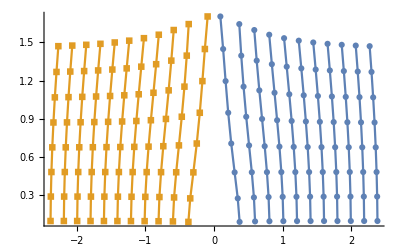

```mathematica
Show[Table[PlotSchQNM[l],{l,2,12}],PlotRange->All]
```

### Create the ℓ=2, m=2, n=0 QNM sequence to an accuracy of 10^-5.

```mathematica
KerrQNMSequence[2,2,0,-5]
```

### Plot the mode frequencies and separation constant values along the ℓ = 2, m = 2, n = 0 sequence .

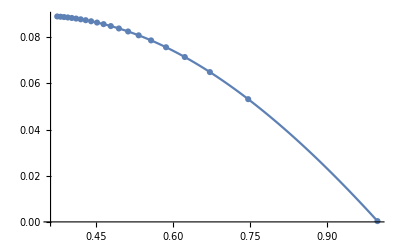

```mathematica
ModePlotOmega[2,2,0]
```

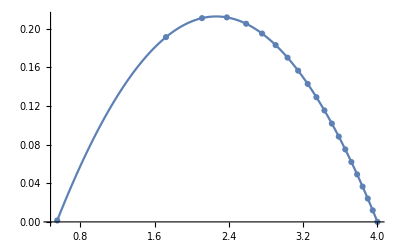

```mathematica
ModePlotA[2,2,0]
```